```mathematica
file="/Users/vpk/Google\ Drive/Jlab/Projects/Mathematica/densities.txt";
Hdata=ReadList[file,{Number,Number,Number,Number,Number}];
X=Hdata[[All,1]];
HProfileu=Hdata[[All,2]];
HForwardu=Hdata[[All,2]];
HProfiled=Hdata[[All,3]];
HForwardd=Hdata[[All,4]];
xmin=1.9924×10^-5;
xmax=0.5;
ymin=0;
ymax=15;
HFu=Interpolation[Thread[{X,HForwardu}],InterpolationOrder->1];
HFd=Interpolation[Thread[{X,HForwardd}],InterpolationOrder->1];
HPu=Interpolation[Thread[{X,HProfileu}],InterpolationOrder->1];
HPd=Interpolation[Thread[{X,HProfiled}],InterpolationOrder->1];
Hu[x_,t_]:=HFu[x]*Exp[HPu[x]*t];
Hd[x_,t_]:=HFd[x]*Exp[HPd[x]*t];

PlotFL=Plot[{HFu[x],HFd[x]},{x,xmin,xmax},PlotRange->{{xmin,xmax},{ymin,ymax}},FrameLabel->{"x","Forward Limit"},PlotLegends->Placed[{u-quark,d-quark},Center],Frame->True,Filling->Axis,ImageSize->Medium,PlotLabel->"Forward Limit"];
PlotPF=Plot[{HPu[x],HPd[x]},{x,xmin,xmax},PlotRange->{{xmin,xmax},{ymin,ymax}},FrameLabel->{"x","Profile FUnction"},PlotLegends->Placed[{u-quark,d-quark},Center],Frame->True,Filling->Axis,ImageSize->Medium,PlotLabel->"Profile Function"];
xx=0.1;
 PlotH=Plot[{Hu[0.1,-t],Hd[0.1,-t]},{t,0,1},FrameLabel->{"-t","H(x=0.1,-t"},PlotLegends->Placed[{u-quark,d-quark},Center],Frame->True,Filling->Axis,ImageSize->Medium,PlotLabel-> "H(x=0.1,-t)"];
PlotHu=DensityPlot[Hu[x,-t],{x,0.1,0.5},{t,0,1},ColorFunction->"SunsetColors",PlotLegends->Automatic];
PlotHd=DensityPlot[Hd[x,-t],{x,0.1,0.5},{t,0,1},ColorFunction->"SunsetColors",PlotLegends->Automatic];
(*GraphicsRow[{PlotFL,PlotPF, PlotH},ImageSize->Large]
*)
```

```mathematica
F3[x_,y_,R_]:=Exp[-(x^2+y^2)/R^2];
F2[x_,y_]:=F3[x,y,R];
R=3;

Col="SunsetColors"; Print[Col]; DensityPlot[F2[x,y],{x,0-5,5},{y,-5,5},ColorFunction->Hue,PlotLegends->Automatic]
Col="SunsetColors"; Print[Col]; DensityPlot[F2[x,y],{x,0-5,5},{y,-5,5},ColorFunction->(Hue[2/5,2/3,#]&),PlotLegends->Automatic] 
Col="GreyLevel"; Print[Col];        DensityPlot[F2[x,y],{x,0-5,5},{y,-5,5},ColorFunction->GrayLevel,        PlotLegends->Automatic]
Col="SunsetColors"; Print[Col]; DensityPlot[F2[x,y],{x,0-5,5},{y,-5,5},ColorFunction->"SunsetColors",PlotLegends->Automatic]
```

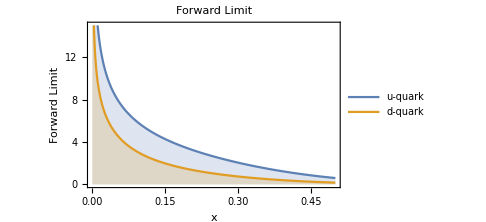

```mathematica
PlotFL
```